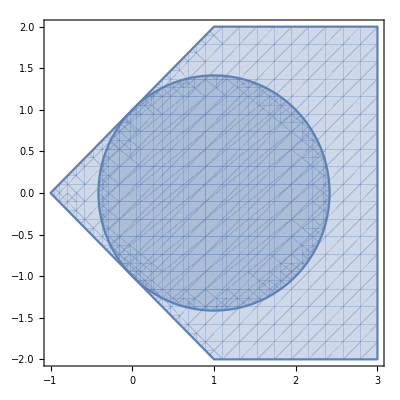

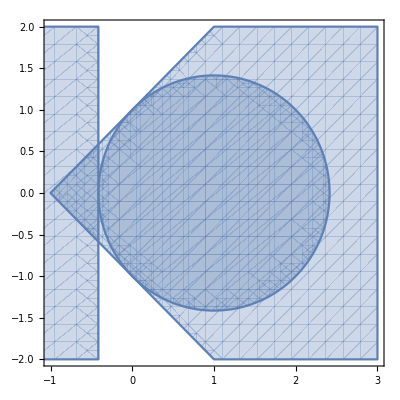

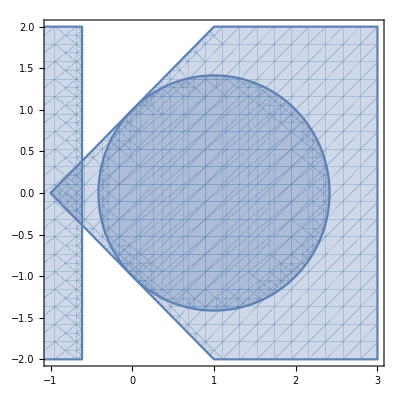

```mathematica
u =0.5;
q[x_]:=(x-1)^2;
lq[x_,u_]:=q[u]+q'[u]*(x-u);
lq[x,0.5];
plt0  = Show[RegionPlot[(y)^2 < (x+1)^2 ,{x,-1,3},{y,-2,2}], RegionPlot[(x-1)^2 + y^2<2,{x,-2,3},{y,-2,2} ]];
plt1 = Show[RegionPlot[(y)^2 < (x+1)^2 ,{x,-1,3},{y,-2,2}], RegionPlot[x<1 - Sqrt[2],{x,-2,3},{y,-2,2} ], RegionPlot[(x-1)^2 + y^2<2,{x,-2,3},{y,-2,2} ]];
plt2 = Show[RegionPlot[(y)^2 < (x+1)^2 ,{x,-1,3},{y,-2,2}], RegionPlot[x<1 - Sqrt[2] - 0.2,{x,-2,3},{y,-2,2} ], RegionPlot[(x-1)^2 + y^2<2,{x,-2,3},{y,-2,2} ]];
plt0
plt1
plt2
```